```mathematica
ClearAll[AcousticModel]
(*Note the-sign in the operator*)
AcousticModel[p_,X_List,ρ_,{Q_,F_}]:=Module[{a,factor},factor=-1/ρ*IdentityMatrix[Length[X]];
a=PiecewiseExpand[Piecewise[{{factor,True}}]];
Inactive[Div][a.Inactive[Grad][p,X],X]-Inactive[Div][F/ρ,X]-Q] (*Source free model*)
AcousticModel[p_,X_List,ρ_]:=Module[{a,factor},factor=-1/ρ*IdentityMatrix[Length[X]];
a=PiecewiseExpand[Piecewise[{{factor,True}}]];
Inactive[Div][a.Inactive[Grad][p,X],X]]
```

```mathematica
TimeAcousticsModel=1/(ρ c^2)*D[p[t,x],{t,2}]+AcousticModel[p[t,x],{x},ρ]
```

({{-1/ρ}}.p[t,x]{x}Inactive){x}Inactive+(p^(2,0)[t,x])/(c^2 ρ)

```mathematica
Subscript[c,air]=QuantityMagnitude[ThermodynamicData["Air","SoundSpeed"]];
Subscript[ρ,air]=QuantityMagnitude[ThermodynamicData["Air","Density"]];
```

```mathematica
TimeAcousticsModel/.{c->Subscript[c,air],ρ->Subscript[ρ,air]}
```

({{-0.830168}}.p[t,x]{x}Inactive){x}Inactive+7.04219×10^-6 p^(2,0)[t,x]

```mathematica
Head[1.5]
```

Real

```mathematica
SoundIntensity[r_Real,p_Real]:=Divide[p,Times[4,Pi,r,r]] (* r is the distance, p is the sound power*)
```

```mathematica
SoundIntensity[5.0,100.0]
```

0.31831

```mathematica
SoundPower[u_Real,z_Real]:=Divide[u^2,z] (* u is the voltage amplitude, and z is the impedance*)
```

```mathematica
SoundPower[6.0,2.0]
```

18.

```mathematica
SoundIntensity[5.0,SoundPower[10.0,1.0]]
```

0.31831

```mathematica
Apply[Plus,10^({78,84,86,98}*0.05)]
```

```mathematica
123177.66089397095
(*sound pressure levels are in decibels, sound pressure values are in micropascals*)
```

```mathematica
AverageSoundPressureLevel[num_List]:=20*Log10[Apply[Plus,10^(num*0.05)]/Length[num]](* decibels*)
```

```mathematica
AverageSoundPressureLevel[{78,84,86,98}]
```

89.7694

```mathematica
EquivalentSoundPressureLevel[num_List]:=10*Log10[Apply[Plus,#[[2]]*10^(#[[1]]*0.1)&/@num]/Apply[Plus,num[[All,2]]]]
```

```mathematica
EquivalentSoundPressureLevel[{{90,10},{70,30}}]
```

84.1078

```mathematica
EquivalentSoundPressureLevel[{{110,40},{500,20},{80,30}}]
```

493.468

```mathematica
PressureValue2PressureLevel[n_Real]:=20*Log10[n/20]
```

```mathematica
PressureValue2PressureLevel[3000.0]
```

43.5218

```mathematica
PressureLevel2PressureValue[n_Real]:=20*10^(n*0.05)
```

```mathematica
PressureLevel2PressureValue[42.0]
```

2517.85

```mathematica
CombinedSoundPowerLevel[num_List]:=10*Log10[Apply[Plus,10^(num*0.1)]]
```

```mathematica
CombinedSoundPowerLevel[{50,60,70,80,90}]
```

90.4575

```mathematica
x={{1,2},{3,4}}
```

{{1,2},{3,4}}

```mathematica
{{1,2},{3,4}}
```

{{1,2},{3,4}}

```mathematica
x[[All,1]]
```

{1,3}

```mathematica
SoundSources={{5,3,10},{6,8,100}}
```

{{5,3,10},{6,8,100}}

```mathematica
{{5,3,10},{6,8,100}}
```

{{5,3,10},{6,8,100}}

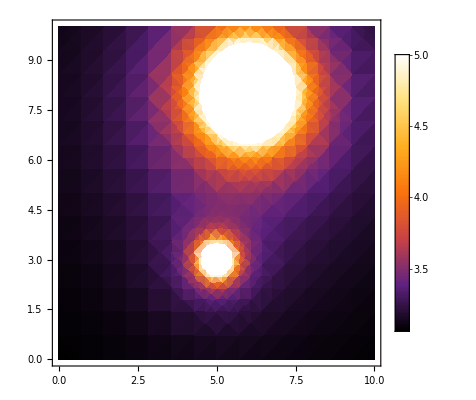

```mathematica
DensityPlot[CombinedSoundPowerLevel[SoundIntensity[Sqrt[(#[[1]]-x)^2+(#[[2]]-y)^2],#[[3]]]&/@SoundSources],{x,0,10},{y,0,10},ColorFunction->"SunsetColors",PlotLegends->Automatic]
```

```mathematica
OmniSoundDensityPlot[soundSources_List]:=DensityPlot[10*Log10[Apply[Plus,10^((Divide[#[[3]],Times[4,Pi,(#[[1]]-x)^2+(#[[2]]-y)^2]]&/@soundSources)*0.1)]],{x,0,10},{y,0,10},ColorFunction->"SunsetColors",PlotLegends->Automatic]
```

```mathematica
OmniSoundDensityPlot[SoundSources]
```

-Graphics-

```mathematica
Manipulate[OmniSoundDensityPlot[{{x1,y1,p1},{x2,y2,p2}}],{x1,0,10,0.1},{y1,0,10,0.1},{p1,0,100,1},{x2,0,10,0.1},{y2,0,10,0.1},{p2,0,100,1}]
```